ξ=ln √s

```mathematica
snew[s_,T_]=Exp[2ArcTanh[T Tanh[Log[√s]]]];
snew[2,0.6]
```

1.5

```mathematica
snew2[s_,T_]=(s(1+T)+(1-T))/(s(1-T)+(1+T));
snew2[2,0.6]
```

1.5

```mathematica
snew2[3,0.5]
```

1.66667

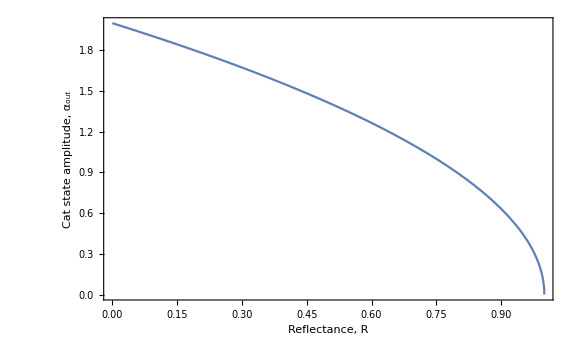

```mathematica
αnew[α_,T_]=√T α;
Plot[αnew[2,1-R],{R,0,1},AxesStyle->Black,ImageSize->Large,Frame->True,FrameStyle->Black,FrameLabel->{"Reflectance, R","Cat state amplitude, α_out","Initial Cat state amplitude, α_in = 2"},LabelStyle->{Black,Large}]
```

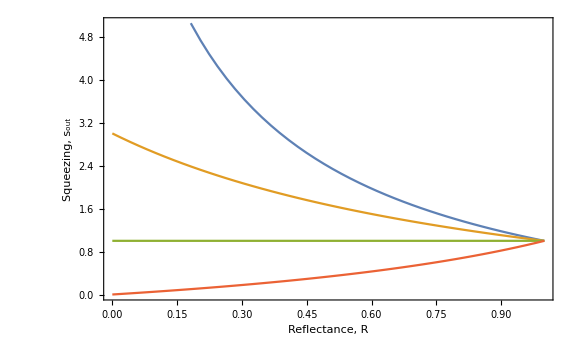

```mathematica
Plot[{snew2[10,1-R],snew2[3,1-R],snew2[1,1-R],snew2[0.001,1-R]},{R,0,1},AxesStyle->Black,ImageSize->Large,Frame->True,FrameStyle->Black,FrameLabel->{"Reflectance, R","Squeezing, s_out","Initial squeezing, s_in = 3"},LabelStyle->{Black,Large}]
```